```mathematica
e1=1.602176634000000 10^-19(*Couloumbs*);
me1=9.1093837015 10^-31 (*kg*);
m1=.19me1(*kg*);
hmev1=4.135667696 10^-12(*meV Second*);
ℏmev1=hmev1/(2π)(*meV Second*);
h1=6.62607015000000 10^-34(*Joule Second*); 
ℏ1=h1/(2π)(*Joule Second*);
ϵ01=8.8541878128000000 10^-12(*Farad/m*);
cs1=299792458 (*m/s*);
ϵr1=11.6(*Relative Silicon Permitivity, Dimensionless*);
ω01=12/ℏmev1;
```

Single dipole potential without overall coefficient

```mathematica
V[x_,y_,xi_,yi_,ϕi_,h_]:=((x-xi)Cos[ϕi]+(y-yi)Sin[ϕi])/(((x-xi)^2+(y-yi)^2+h^2)^(3/2));
```

Second order derivatives

```mathematica
Vxx[xi_,yi_,ϕi_,h_]=(3 (xi (3 h^2-2 xi^2+3 yi^2) Cos[ϕi]+yi (h^2-4 xi^2+yi^2) Sin[ϕi]))/((h^2+xi^2+yi^2)^(7/2));
Vxy[xi_,yi_,ϕi_,h_]=(3 (yi (h^2-4 xi^2+yi^2) Cos[ϕi]+xi (h^2+xi^2-4 yi^2) Sin[ϕi]))/((h^2+xi^2+yi^2)^(7/2));
Vyy[xi_,yi_,ϕi_,h_]=(3 (xi (h^2+xi^2-4 yi^2) Cos[ϕi]+yi (3 h^2+3 xi^2-2 yi^2) Sin[ϕi]))/((h^2+xi^2+yi^2)^(7/2));
```

Below is V_xx-V_yy

```mathematica
Vxxyy[xi_,yi_,ϕi_,h_]=(3 (xi (2 h^2-3 xi^2+7 yi^2) Cos[ϕi]+yi (-2 h^2-7 xi^2+3 yi^2) Sin[ϕi]))/((h^2+xi^2+yi^2)^(7/2));
```

4th order derivatives

```mathematica
V4x[xi_,yi_,ϕi_,h_]:=D[D[D[D[V[x,y,xi,yi,ϕi,h],x],x],x],x]/.{x->0,y->0};
V3x1y[xi_,yi_,ϕi_,h_]:=D[D[D[D[V[x,y,xi,yi,ϕi,h],x],x],x],y]/.{x->0,y->0};
V2x2y[xi_,yi_,ϕi_,h_]:=D[D[D[D[V[x,y,xi,yi,ϕi,h],x],x],y],y]/.{x->0,y->0};
V1x3y[xi_,yi_,ϕi_,h_]:=D[D[D[D[V[x,y,xi,yi,ϕi,h],x],y],y],y]/.{x->0,y->0};
V4y[xi_,yi_,ϕi_,h_]:=D[D[D[D[V[x,y,xi,yi,ϕi,h],y],y],y],y]/.{x->0,y->0};
```

```mathematica
V2x2y[xi,yi,ϕi,h]//Simplify
```

1/((h^2+xi^2+yi^2)^(11/2))15 (xi (-3 h^4+4 xi^4-41 xi^2 yi^2+18 yi^4+h^2 (xi^2+15 yi^2)) Cos[ϕi]+yi (-3 h^4+18 xi^4-41 xi^2 yi^2+4 yi^4+h^2 (15 xi^2+yi^2)) Sin[ϕi])

```mathematica
V3x1y[xi,yi,ϕi,h]//Simplify
```

1/((h^2+xi^2+yi^2)^(11/2))(-45 yi (h^4+8 xi^4-12 xi^2 yi^2+yi^4+2 h^2 (-6 xi^2+yi^2)) Cos[ϕi]+15 xi (-3 h^4+4 xi^4-41 xi^2 yi^2+18 yi^4+h^2 (xi^2+15 yi^2)) Sin[ϕi])

```mathematica
V1x3y[xi,yi,ϕi,h]//Simplify
```

1/((h^2+xi^2+yi^2)^(11/2))(15 yi (-3 h^4+18 xi^4-41 xi^2 yi^2+4 yi^4+h^2 (15 xi^2+yi^2)) Cos[ϕi]-45 xi (h^4+xi^4-12 xi^2 yi^2+8 yi^4+2 h^2 (xi^2-6 yi^2)) Sin[ϕi])

```mathematica
V4y[xi,yi,ϕi,h]//Simplify
```

-1/((h^2+xi^2+yi^2)^(11/2))15 (3 xi (h^4+xi^4-12 xi^2 yi^2+8 yi^4+2 h^2 (xi^2-6 yi^2)) Cos[ϕi]+yi (15 h^4+15 xi^4-40 xi^2 yi^2+8 yi^4+10 h^2 (3 xi^2-4 yi^2)) Sin[ϕi])

```mathematica
(V3x1y[xi,yi,ϕi,h]+V1x3y[xi,yi,ϕi,h])//Simplify
```

-1/((h^2+xi^2+yi^2)^(11/2))15 (yi (6 h^4+6 xi^4+5 xi^2 yi^2-yi^4+h^2 (-51 xi^2+5 yi^2)) Cos[ϕi]+xi (6 h^4-xi^4+5 xi^2 yi^2+6 yi^4+h^2 (5 xi^2-51 yi^2)) Sin[ϕi])

```mathematica
V4x[xi_,yi_,ϕi_,h_]=1/((h^2+xi^2+yi^2)^(11/2))15 (xi (-3 h^4+4 xi^4-41 xi^2 yi^2+18 yi^4+h^2 (xi^2+15 yi^2)) Cos[ϕi]+yi (-3 h^4+18 xi^4-41 xi^2 yi^2+4 yi^4+h^2 (15 xi^2+yi^2)) Sin[ϕi]);
V3x1y[xi_,yi_,ϕi_,h_]=1/((h^2+xi^2+yi^2)^(11/2))(-45 yi (h^4+8 xi^4-12 xi^2 yi^2+yi^4+2 h^2 (-6 xi^2+yi^2)) Cos[ϕi]+15 xi (-3 h^4+4 xi^4-41 xi^2 yi^2+18 yi^4+h^2 (xi^2+15 yi^2)) Sin[ϕi]);
V1x3y[xi_,yi_,ϕi_,h_]=1/((h^2+xi^2+yi^2)^(11/2))(15 yi (-3 h^4+18 xi^4-41 xi^2 yi^2+4 yi^4+h^2 (15 xi^2+yi^2)) Cos[ϕi]-45 xi (h^4+xi^4-12 xi^2 yi^2+8 yi^4+2 h^2 (xi^2-6 yi^2)) Sin[ϕi]);
V4y[xi_,yi_,ϕi_,h_]=-1/((h^2+xi^2+yi^2)^(11/2))15 (3 xi (h^4+xi^4-12 xi^2 yi^2+8 yi^4+2 h^2 (xi^2-6 yi^2)) Cos[ϕi]+yi (15 h^4+15 xi^4-40 xi^2 yi^2+8 yi^4+10 h^2 (3 xi^2-4 yi^2)) Sin[ϕi]);
V3x1y1x3y[xi_,yi_,ϕi_,h_]=-1/((h^2+xi^2+yi^2)^(11/2))15 (yi (6 h^4+6 xi^4+5 xi^2 yi^2-yi^4+h^2 (-51 xi^2+5 yi^2)) Cos[ϕi]+xi (6 h^4-xi^4+5 xi^2 yi^2+6 yi^4+h^2 (5 xi^2-51 yi^2)) Sin[ϕi]);
```

Generate variable strings and potential induced energy fluctuation functions

```mathematica
num[n_]:=Range[1,n]
vars[n_]:=ToExpression[Table[{"x"<>ToString[i],"y"<>ToString[i],"ϕ"<>ToString[i]},{i,1,n}]];
δEx[n_,l_,h_]:=l^2/2 Sum[(Vxxyy[vars[n][[i,1]],vars[n][[i,2]],vars[n][[i,3]],h]),{i,1,n}];
δEy[n_,l_,h_]:=l^2 Sum[Vxy[vars[n][[i,1]],vars[n][[i,2]],vars[n][[i,3]],h],{i,1,n}];
δEx5[n_,l_,h_]:=l^4/16 Sum[V4x[vars[n][[i,1]],vars[n][[i,2]],vars[n][[i,3]],h],{i,1,n}];
δEy5[n_,l_,h_]:=l^4/8 Sum[V3x1y1x3y[vars[n][[i,1]],vars[n][[i,2]],vars[n][[i,3]],h],{i,1,n}];
```

Energy with noise expansion to 3rd term (Quadrupole term)

```mathematica
En[n_,h_,l_,d_,Ez_,Ex_,Ey_]:=√(Ez^2+(Ex+(e1^2 d 10^9)/(4π ϵ01 ϵr1)δEx[n,l,h])^2+(Ey+(e1^2 d 10^9)/(4π ϵ01 ϵr1)δEy[n,l,h])^2)
```

Energy with noise expansion to 5th term (Hexadecapole term)

```mathematica
En5[n_,h_,l_,d_,Ez_,Ex_,Ey_]:=√(Ez^2+(Ex+(e1^2 d 10^9)/(4π ϵ01 ϵr1)(δEx[n,l,h]+δEx5[n,l,h]))^2+(Ey+(e1^2 d 10^9)/(4π ϵ01 ϵr1)(δEy[n,l,h]+δEy5[n,l,h]))^2)
```

Monte Carlo simulation including Quadrupole term

```mathematica
monte1[n_,h_,l_,d_,Ez_,Ex_,Ey_,A_,montepoints_]:=Catch[Do[tab=Table[Table[{RandomReal[{(-√A)/2,(√A)/2}],RandomReal[{(-√A)/2,(√A)/2}],RandomReal[{0,2π}]},{i,1,n}],{k,1,montepoints}];
ESqAvg1=1/montepoints∑_(i=1)^montepoints (En[n,h,l,d,Ez,Ex,Ey]^2/.{Evaluate[Sequence@@(xReplace[i,#]&/@num[n])],Evaluate[Sequence@@(yReplace[i,#]&/@num[n])],Evaluate[Sequence@@(ϕReplace[i,#]&/@num[n])]});
EAvgSq1=(1/montepoints∑_(i=1)^montepoints (En[n,h,l,d,Ez,Ex,Ey]/.{Evaluate[Sequence@@(xReplace[i,#]&/@num[n])],Evaluate[Sequence@@(yReplace[i,#]&/@num[n])],Evaluate[Sequence@@(ϕReplace[i,#]&/@num[n])]}))^2;
Throw[√2 ℏ1/(√(ESqAvg1-EAvgSq1))10^9]
,1]]
```

Monte Carlo simulation including Quadrupole and Hexadecapole term

```mathematica
monte2[n_,h_,l_,d_,Ez_,Ex_,Ey_,A_,montepoints_]:=Catch[Do[tab=Table[Table[{RandomReal[{(-√A)/2,(√A)/2}],RandomReal[{(-√A)/2,(√A)/2}],RandomReal[{0,2π}]},{i,1,n}],{k,1,montepoints}];
ESqAvg2=1/montepoints∑_(i=1)^montepoints (En5[n,h,l,d,Ez,Ex,Ey]^2/.{Evaluate[Sequence@@(xReplace[i,#]&/@num[n])],Evaluate[Sequence@@(yReplace[i,#]&/@num[n])],Evaluate[Sequence@@(ϕReplace[i,#]&/@num[n])]});
EAvgSq2=(1/montepoints∑_(i=1)^montepoints (En5[n,h,l,d,Ez,Ex,Ey]/.{Evaluate[Sequence@@(xReplace[i,#]&/@num[n])],Evaluate[Sequence@@(yReplace[i,#]&/@num[n])],Evaluate[Sequence@@(ϕReplace[i,#]&/@num[n])]}))^2;
Throw[√2 ℏ1/(√(ESqAvg2-EAvgSq2))10^9]
,1]]
```

Test it out

```mathematica
monte1[10,100,10,.1,0,0,0,100^2,1000]
```

83.1678

```mathematica
monte2[10,100,10,.1,0,0,0,100^2,1000]
```

84.1078

Perform multiple Monte Carlo simulations and generate histogram considering both noise expansion orders.

```mathematica
Tquad=Table[monte1[10,100,10,.1,0,0,0,100^2,1000],{m,0,100}];
```

```mathematica
T5=Table[monte2[10,100,10,.1,0,0,0,100^2,1000],{m,0,100}];
```

```mathematica
Export["C:\\Users\\KestnerPC3\\Box\\UMBC\\Research\\Orbital Qubit\\nb\\Core\\Post 429\\T2 Calcuations\\p orbital noise data\\TQuadTermOnly.csv",Tquad,"List"];
Export["C:\\Users\\KestnerPC3\\Box\\UMBC\\Research\\Orbital Qubit\\nb\\Core\\Post 429\\T2 Calcuations\\p orbital noise data\\TQuadTermOnly.csv",T5,"List"];
```

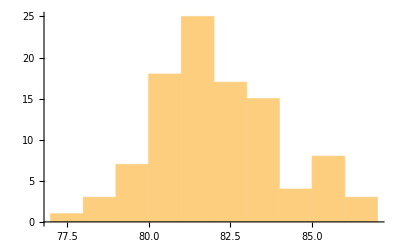

```mathematica
Histogram[Tquad]
```

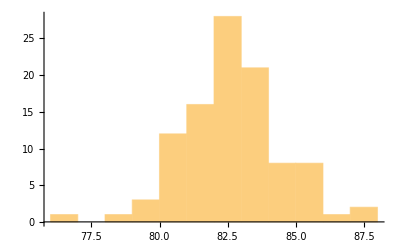

```mathematica
Histogram[T5]
```

```mathematica
TQuad=Import["C:\\Users\\KestnerPC3\\Box\\UMBC\\Research\\Orbital Qubit\\nb\\Core\\Post 429\\T2 Calcuations\\p orbital noise data\\TQuadTermOnly.csv","List"];
```

```mathematica
TQuadandHex=Import["C:\\Users\\KestnerPC3\\Box\\UMBC\\Research\\Orbital Qubit\\nb\\Core\\Post 429\\T2 Calcuations\\p orbital noise data\\TQuadTermAnd5Term.csv","List"];
```

```mathematica
Histogram[TQuad]
```

-Graphics-

```mathematica
Mean[TQuad]
```

82.1344

```mathematica
StandardDeviation[TQuad]
```

1.85535

```mathematica
Histogram[TQuadandHex]
```

-Graphics-

```mathematica
Mean[TQuadandHex]
```

82.6234

```mathematica
StandardDeviation[TQuadandHex]
```

1.81805